```mathematica
Distance[n_, p_] := Module[ {threshold, digits, position, found, nextPower, result},
  If [n == 0, Return[0]];
  (* Initialize some precomputed local varables *)
  threshold = (p - 1)/2;
  digits = IntegerDigits[n, p];
  
  (* find the first digit above the threshold *)
  found = -1;
  For[ position = 1, position <= Length[digits], position++,
   If [ digits [[position]] > threshold,
    found = position; Break[]
    ]
   ];
  
  (* if we didn't find a digit, then the distance is zero *)
  If [found == -1, Return[0]];
  
  (* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
  If we would not count these then we would end up with a new value which is still not p-good (due
  to the carrying) *)
  While[ found > 1,
   If [ digits [[found - 1]] == threshold, found --, Break[]]
   ];
  
  (* if we have gone all the way to the start*)
  If[found == 1,
   Block[{},
    nextPower = p^(Length[digits]);
    Return[nextPower - n]
    ]
   ];
  
  
  nextPower = p^(Length[digits] + 1 - found);
  Return[nextPower - FromDigits[Take[digits, -(Length[digits] + 1 - found)], p]]
  ]
```

```mathematica
TailSearch[start_, end_, primes_] := Module[
{result, current,  maxdist, hops, previous, convert},
result = {};
current=start;
hops=0;
Monitor[
previous={1,1,1,1};
While[current ≤ end,
(*Print[current];*)
hops++;
maxdist = Max[ParallelTable[Distance[current, p], {p, primes}]];
If[maxdist==0,

convert=IntegerDigits[current,First[primes]];
If[ListEndsWith[previous, convert],
Print[convert];
AppendTo[result,convert];
previous=convert
];
current +=Max[Min[ParallelTable[Distance[current+1, p], {p, primes}]],1];
,
current += maxdist;
];
],
{primes,hops, Length[result],N[Log[10,current]]}
];

PrintTemporary [{primes,result,hops}];
Return [{primes,result,hops}];
]
```

```mathematica
TailSearch[0,10^10000,{3,5,7}]
```

{1,1,1,1,1,1,1,0,1,0,0,0,0,0,1,0,1,0,1,1,1,0,1,0,0,0,1,0,0,1,1,1,1,1,1}

```mathematica
TailSearch[0,10^100,{3,5,7}]
```

{{3,5,7},{{0},{1,0,0,1,0,0,0},{1,0,0,1,0,1,1,0,1,0,0,1,0,0,0,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0,1,1,0,0,0,1,1,1,0,1,0,0,1,0,0,0}},493845}

```mathematica
TailSearch[10^116,10^1000,{3,5,7}]
```

$Aborted

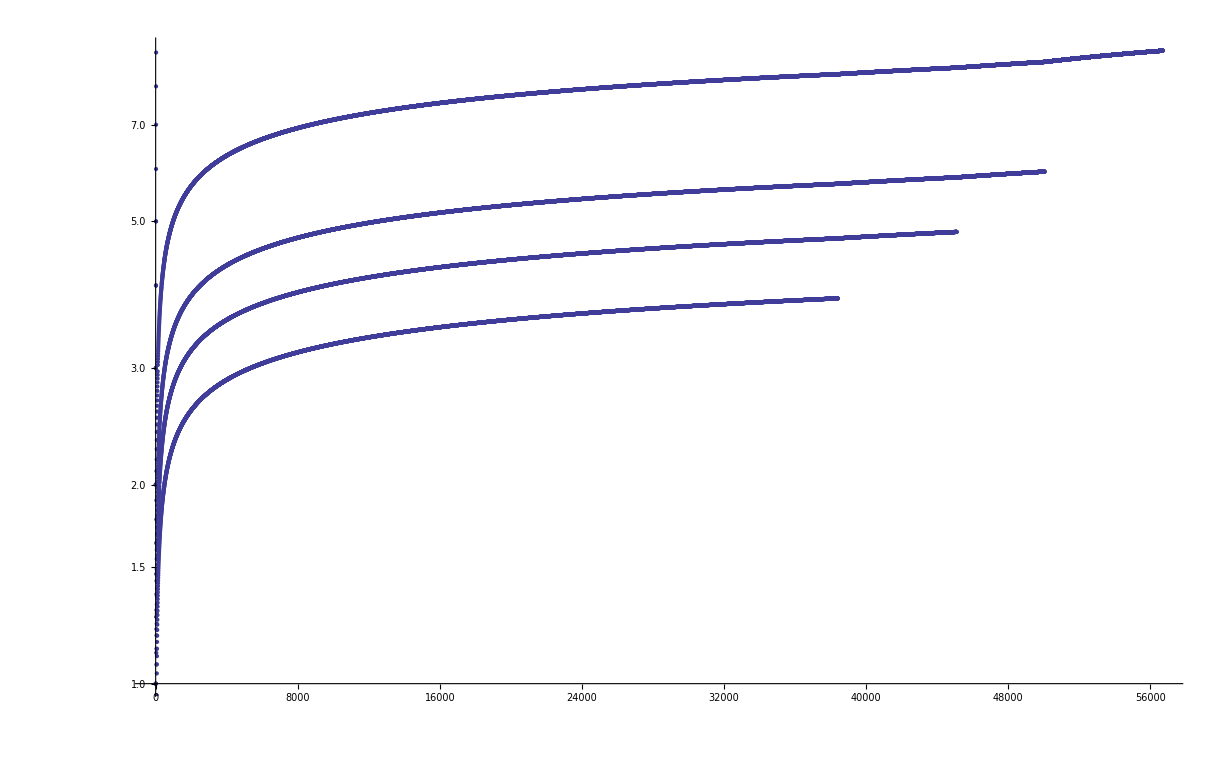

```mathematica
ListLogPlot[Map[#[[1]]&,Sort[Flatten[Table[Table[{Log[p,i], {p^i,i}},{i,1,Floor[Log[p,10^10000]]}],{p,{3,5,7,11}}],1]]]]
```

```mathematica
Map[#[[2,1]]&,Sort[Flatten[Table[Table[{p^i, {p^i,i}},{i,0,Log[p,10^100]}],{p,{3,5,7,11}}],1]]]
```

{1,1,1,1,3,5,7,9,11,25,27,49,81,121,125,243,343,625,729,1331,2187,2401,3125,6561,14641,15625,16807,19683,59049,78125,117649,161051,177147,390625,531441,823543,1594323,1771561,1953125,4782969,5764801,9765625,14348907,19487171,40353607,43046721,48828125,129140163,214358881,244140625,282475249,387420489,1162261467,1220703125,1977326743,2357947691,3486784401,6103515625,10460353203,13841287201,25937424601,30517578125,31381059609,94143178827,96889010407,152587890625,282429536481,285311670611,678223072849,762939453125,847288609443,2541865828329,3138428376721,3814697265625,4747561509943,7625597484987,19073486328125,22876792454961,33232930569601,34522712143931,68630377364883,95367431640625,205891132094649,232630513987207,379749833583241,476837158203125,617673396283947,1628413597910449,1853020188851841,2384185791015625,4177248169415651,5559060566555523,11398895185373143,11920928955078125,16677181699666569,45949729863572161,50031545098999707,59604644775390625,79792266297612001,150094635296999121,298023223876953125,450283905890997363,505447028499293771,558545864083284007,1350851717672992089,1490116119384765625,3909821048582988049,4052555153018976267,5559917313492231481,7450580596923828125,12157665459056928801,27368747340080916343,36472996377170786403,37252902984619140625,61159090448414546291,109418989131512359209,186264514923095703125,191581231380566414401,328256967394537077627,672749994932560009201,931322574615478515625,984770902183611232881,1341068619663964900807,2954312706550833698643,4656612873077392578125,7400249944258160101211,8862938119652501095929,9387480337647754305649,23283064365386962890625,26588814358957503287787,65712362363534280139543,79766443076872509863361,81402749386839761113321,116415321826934814453125,239299329230617529590083,459986536544739960976801,582076609134674072265625,717897987691852588770249,895430243255237372246531,2153693963075557766310747,2910383045673370361328125,3219905755813179726837607,6461081889226673298932241,9849732675807611094711841,14551915228366851806640625,19383245667680019896796723,22539340290692258087863249,58149737003040059690390169,72759576141834259033203125,108347059433883722041830251,157775382034845806615042743,174449211009120179071170507,363797880709171295166015625,523347633027360537213511521,1104427674243920646305299201,1191817653772720942460132761,1570042899082081611640534563,1818989403545856475830078125,4710128697246244834921603689,7730993719707444524137094407,9094947017729282379150390625,13109994191499930367061460371,14130386091738734504764811067,42391158275216203514294433201,45474735088646411895751953125,54116956037952111668959660849,127173474825648610542883299603,144209936106499234037676064081,227373675443232059478759765625,378818692265664781682717625943,381520424476945831628649898809,1136868377216160297393798828125,1144561273430837494885949696427,1586309297171491574414436704891,2651730845859653471779023381601,3433683820292512484657849089281,5684341886080801486968994140625,10301051460877537453973547267843,17449402268886407318558803753801,18562115921017574302453163671207,28421709430404007434844970703125,30903154382632612361920641803529,92709463147897837085761925410587,129934811447123020117172145698449,142108547152020037174224853515625,191943424957750480504146841291811,278128389443693511257285776231761,710542735760100185871124267578125,834385168331080533771857328695283,909543680129861140820205019889143,2111377674535255285545615254209921,2503155504993241601315571986085849,3552713678800500929355621337890625,6366805760909027985741435139224001,7509466514979724803946715958257547,17763568394002504646778106689453125,22528399544939174411840147874772641,23225154419887808141001767796309131,44567640326363195900190045974568007,67585198634817523235520443624317923,88817841970012523233890533447265625,202755595904452569706561330872953769,255476698618765889551019445759400441,311973482284542371301330321821976049,444089209850062616169452667236328125,608266787713357709119683992618861307,1824800363140073127359051977856583921,2183814375991796599109312252753832343,2220446049250313080847263336181640625,2810243684806424785061213903353404851,5474401089420219382077155933569751763,11102230246251565404236316680908203125,15286700631942576193765185769276826401,16423203268260658146231467800709255289,30912680532870672635673352936887453361,49269609804781974438694403402127765867,55511151231257827021181583404541015625,107006904423598033356356300384937784807,147808829414345923316083210206383297601,277555756156289135105907917022705078125,340039485861577398992406882305761986971,443426488243037769948249630619149892803,749048330965186233494494102694564493649,1330279464729113309844748891857449678409,1387778780781445675529539585113525390625,3740434344477351388916475705363381856681,3990838394187339929534246675572349035227,5243338316756303634461458718861951455543,6938893903907228377647697925567626953125,11972515182562019788602740026717047105681,34694469519536141888238489627838134765625,35917545547686059365808220080151141317043,36703368217294125441230211032033660188801,41144777789250865278081232758997200423491,107752636643058178097424660240453423951129,173472347597680709441192448139190673828125,256923577521058878088611477224235621321607,323257909929174534292273980721360271853387,452592555681759518058893560348969204658401,867361737988403547205962240695953369140625,969773729787523602876821942164080815560161,1798465042647412146620280340569649349251249,2909321189362570808630465826492242446680483,4336808689942017736029811203479766845703125,4978518112499354698647829163838661251242411,8727963568087712425891397479476727340041449,12589255298531885026341962383987545444758743,21684043449710088680149056017398834228515625,26183890704263137277674192438430182020124347,54763699237492901685126120802225273763666521,78551672112789411833022577315290546060373041,88124787089723195184393736687912818113311201,108420217248550443400745280086994171142578125,235655016338368235499067731945871638181119123,542101086242752217003726400434970855712890625,602400691612421918536387328824478011400331731,616873509628062366290756156815389726793178407,706965049015104706497203195837614914543357369,2120895147045314119491609587512844743630072107,2710505431213761085018632002174854278564453125,4318114567396436564035293097707728087552248849,6362685441135942358474828762538534230890216321,6626407607736641103900260617069258125403649041,13552527156068805425093160010874271392822265625,19088056323407827075424486287615602692670648963,30226801971775055948247051683954096612865741943,57264168970223481226273458862846808078011946889,67762635780344027125465800054371356964111328125,72890483685103052142902866787761839379440139451,171792506910670443678820376588540424234035840667,211587613802425391637729361787678676290060193601,338813178901720135627329000271856784820556640625,515377520732011331036461129765621272702107522001,801795320536133573571931534665380233173841533961,1481113296616977741464105532513750734030421355207,1546132562196033993109383389296863818106322566003,1694065894508600678136645001359283924102783203125,4638397686588101979328150167890591454318967698009,8470329472543003390683225006796419620513916015625,8819748525897469309291246881319182564912256873571,10367793076318844190248738727596255138212949486449,13915193059764305937984450503671774362956903094027,41745579179292917813953351511015323088870709282081,42351647362715016953416125033982098102569580078125,72574551534231909331741171093173785967490646405143,97017233784872162402203715694511008214034825609281,125236737537878753441860054533045969266612127846243,211758236813575084767080625169910490512847900390625,375710212613636260325580163599137907799836383538729,508021860739623365322188197652216501772434524836001,1058791184067875423835403125849552452564239501953125,1067189571633593786424240872639621090354383081702091,1127130637840908780976740490797413723399509150616187,3381391913522726342930221472392241170198527451848561,3556153025177363557255317383565515512407041673852007,5293955920339377119177015629247762262821197509765625,10144175740568179028790664417176723510595582355545683,11739085287969531650666649599035831993898213898723001,24893071176241544900787221684958608586849291716964049,26469779601696885595885078146238811314105987548828125,30432527221704537086371993251530170531786747066637049,91297581665113611259115979754590511595360241199911147,129129938167664848157333145589394151932880352885953011,132348898008484427979425390731194056570529937744140625,174251498233690814305510551794710260107945042018748343,273892744995340833777347939263771534786080723599733441,661744490042422139897126953655970282852649688720703125,821678234986022501332043817791314604358242170799200323,1219760487635835700138573862562971820755615294131238401,1420429319844313329730664601483335671261683881745483121,2465034704958067503996131453373943813074726512397600969,3308722450212110699485634768279851414263248443603515625,7395104114874202511988394360121831439224179537192802907,8538323413450849900970017037940802745289307058918668807,15624722518287446627037310616316692383878522699200314331,16543612251060553497428173841399257071316242218017578125,22185312344622607535965183080365494317672538611578408721,59768263894155949306790119265585619217025149412430681649,66555937033867822607895549241096482953017615834735226163,82718061255302767487140869206996285356581211090087890625,171871947701161912897410416779483616222663749691203457641,199667811101603467823686647723289448859052847504205678489,413590306276513837435704346034981426782906055450439453125,418377847259091645147530834859099334519176045887014771543,599003433304810403471059943169868346577158542512617035467,1797010299914431210413179829509605039731475627537851106401,1890591424712781041871514584574319778449301246603238034051,2067951531382569187178521730174907133914530277252197265625,2928644930813641516032715844013695341634232321209103400801,5391030899743293631239539488528815119194426882613553319203,10339757656912845935892608650874535669572651386260986328125,16173092699229880893718618465586445357583280647840659957609,20500514515695490612229010908095867391439626248463723805607,20796505671840591460586660430317517562942313712635618374561,48519278097689642681155855396759336072749841943521979872827,51698788284564229679463043254372678347863256931304931640625,143503601609868434285603076356671071740077383739246066639249,145557834293068928043467566190278008218249525830565939618481,228761562390246506066453264733492693192365450838991802120171,258493941422821148397315216271863391739316284656524658203125,436673502879206784130402698570834024654748577491697818855443,1004525211269079039999221534496697502180541686174722466474743,1292469707114105741986576081359316958696581423282623291015625,1310020508637620352391208095712502073964245732475093456566329,2516377186292711566730985912068419625116019959228909823321881,3930061525912861057173624287137506221892737197425280369698987,6462348535570528709932880406796584793482907116413116455078125,7031676478883553279994550741476882515263791803223057265323201,11790184577738583171520872861412518665678211592275841109096961,27680149049219827234040845032752615876276219551518008056540691,32311742677852643549664402033982923967414535582065582275390625,35370553733215749514562618584237555997034634776827523327290883,49221735352184872959961855190338177606846542622561400857262407,106111661199647248543687855752712667991103904330482569981872649,161558713389263217748322010169914619837072677910327911376953125,304481639541418099574449295360278774639038415066698088621947601,318334983598941745631063567258138003973311712991447709945617947,344552147465294110719732986332367243247925798357929806000836849,807793566946316088741610050849573099185363389551639556884765625,955004950796825236893190701774414011919935138974343129836853841,2411865032257058775038130904326570702735480588505508642005857943,2865014852390475710679572105323242035759805416923029389510561523,3349298034955599095318942248963066521029422565733678974841423611,4038967834731580443708050254247865495926816947758197784423828125,8595044557171427132038716315969726107279416250769088168531684569,16883055225799411425266916330285994919148364119538560494041005601,20194839173657902218540251271239327479634084738790988922119140625,25785133671514281396116148947909178321838248752307264505595053707,36842278384511590048508364738593731731323648223070468723255659721,77355401014542844188348446843727534965514746256921793516785161121,100974195868289511092701256356196637398170423693954944610595703125,118181386580595879976868414312001964434038548836769923458287039207,232066203043628532565045340531182604896544238770765380550355483363,405265062229627490533592012124531049044560130453775155955812256931,504870979341447555463506281780983186990852118469774723052978515625,696198609130885597695136021593547814689632716312296141651066450089,827269706064171159838078900184013751038269841857389464208009274449,2088595827392656793085408064780643444068898148936888424953199350267,2524354896707237777317531408904915934954260592348873615264892578125,4457915684525902395869512133369841539490161434991526715513934826241,5790887942449198118866552301288096257267888893001726249456064921143,6265787482177970379256224194341930332206694446810665274859598050801,12621774483536188886587657044524579674771302961744368076324462890625,18797362446533911137768672583025790996620083340431995824578794152403,40536215597144386832065866109016673800875222251012083746192454448001,49037072529784926354564633467068256934391775784906793870653283088651,56392087339601733413306017749077372989860250021295987473736382457209,63108872417680944432938285222622898373856514808721840381622314453125,169176262018805200239918053247232118969580750063887962421209147371627,283753509180010707824461062763116716606126555757084586223347181136007,315544362088404722164691426113114491869282574043609201908111572265625,507528786056415600719754159741696356908742250191663887263627442114881,539407797827634189900210968137750826278309533633974732577186113975161,1522586358169246802159262479225089070726226750574991661790882326344643,1577721810442023610823457130565572459346412870218046009540557861328125,1986274564260074954771227439341817016242885890299592103563430267952049,4567759074507740406477787437675267212178680251724974985372646979033929,5933485776103976088902320649515259089061404869973722058349047253726771,7888609052210118054117285652827862296732064351090230047702789306640625,13703277223523221219433362313025801636536040755174924956117940937101787,13903921949820524683398592075392719113700201232097144724944011875664343,39443045261050590270586428264139311483660321755451150238513946533203125,41109831670569663658300086939077404909608122265524774868353822811305361,65268343537143736977925527144667849979675453569710942641839519790994481,97327453648743672783790144527749033795901408624680013074608083129650401,123329495011708990974900260817232214728824366796574324605061468433916083,197215226305252951352932141320696557418301608777255751192569732666015625,369988485035126972924700782451696644186473100389722973815184405301748249,681292175541205709486531011694243236571309860372760091522256581907552807,717951778908581106757180798591346349776429989266820369060234717700939291,986076131526264756764660706603482787091508043886278755962848663330078125,1109965455105380918774102347355089932559419301169168921445553215905244747,3329896365316142756322307042065269797678257903507506764336659647715734241,4769045228788439966405717081859702655999169022609320640655796073352869649,4930380657631323783823303533017413935457540219431393779814243316650390625,7897469567994392174328988784504809847540729881935024059662581894710332201,9989689095948428268966921126195809393034773710522520293009978943147202723,24651903288156618919116517665087069677287701097156968899071216583251953125,29969067287845284806900763378587428179104321131567560879029936829441608169,33383316601519079764840019573017918591994183158265244484590572513470087543,86872165247938313917618876629552908322948028701285264656288400841813654211,89907201863535854420702290135762284537312963394702682637089810488324824507,123259516440783094595582588325435348386438505485784844495356082916259765625,233683216210633558353880137011125430143959282107856711392134007594290612801,269721605590607563262106870407286853611938890184108047911269431464974473521,616297582203915472977912941627176741932192527428924222476780414581298828125,809164816771822689786320611221860560835816670552324143733808294394923420563,955593817727321453093807642925081991552428315714137911219172409259950196321,1635782513474434908477160959077878011007714974754996979744938053160034289607,2427494450315468069358961833665581682507450011656972431201424883184770261689,3081487911019577364889564708135883709660962637144621112383902072906494140625,7282483350946404208076885500996745047522350034970917293604274649554310785067,10511531995000535984031884072175901907076711472855517023410896501859452159531,11450477594321044359340126713545146077054004823284978858214566372120240027249,15407439555097886824447823540679418548304813185723105561919510364532470703125,21847450052839212624230656502990235142567050104912751880812823948662932355201,65542350158517637872691969508970705427701150314738255642438471845988797065603,77037197775489434122239117703397092741524065928615527809597551822662353515625,80153343160247310515380886994816022539378033762994852007501964604841680190743,115626851945005895824350724793934920977843826201410687257519861520453973754841,196627050475552913618075908526912116283103450944214766927315415537966391196809,385185988877447170611195588516985463707620329643077639047987759113311767578125,561073402121731173607666208963712157775646236340963964052513752233891761335201,589881151426658740854227725580736348849310352832644300781946246613899173590427,1271895371395064854067857972733284130756282088215517559832718476724993711303251,1769643454279976222562683176742209046547931058497932902345838739841697520771281,1925929944387235853055977942584927318538101648215388195239938795566558837890625,3927513814852118215253663462745985104429523654386747748367596265637242329346407,5308930362839928667688049530226627139643793175493798707037516219525092562313843,9629649721936179265279889712924636592690508241076940976199693977832794189453125,13990849085345713394746437700066125438319102970370693158159903243974930824335761,15926791088519786003064148590679881418931379526481396121112548658575277686941529,27492596703964827506775644239221895731006665580707234238573173859460696305424849,47780373265559358009192445772039644256794138579444188363337645975725833060824587,48148248609680896326399448564623182963452541205384704880998469889163970947265625,143341119796678074027577337316118932770382415738332565090012937927177499182473761,153899339938802847342210814700727379821510132674077624739758935683724239067693371,192448176927753792547429509674553270117046659064950639670012217016224874137973943,240741243048404481631997242823115914817262706026923524404992349445819854736328125,430023359390034222082732011948356798311147247214997695270038813781532497547421283,1203706215242022408159986214115579574086313530134617622024961747229099273681640625,1290070078170102666248196035845070394933441741644993085810116441344597492642263849,1347137238494276547832006567721872890819326613454654477690085519113574118965817601,1692892739326831320764318961708001178036611459414853872137348292520966629744627081,3870210234510307998744588107535211184800325224934979257430349324033792477926791547,6018531076210112040799931070577897870431567650673088110124808736145496368408203125,9429960669459935834824045974053110235735286294182581343830598633795018832760723207,11610630703530923996233764322605633554400975674804937772291047972101377433780374641,18621820132595144528407508578788012958402726053563392593510831217730632927190897891,30092655381050560203999655352889489352157838253365440550624043680727481842041015625,34831892110592771988701292967816900663202927024414813316873143916304132301341123923,66009724686219550843768321818371771650147004059278069406814190436565131829325062449,104495676331778315966103878903450701989608781073244439950619431748912396904023371769,150463276905252801019998276764447446760789191266827202753120218403637409210205078125,204840021458546589812482594366668142542429986589197318528619143395036962199099876801,313487028995334947898311636710352105968826343219733319851858295246737190712070115307,462068072803536855906378252728602401551029028414946485847699333055955922805275437143,752316384526264005099991383822237233803945956334136013765601092018187046051025390625,940461086986004843694934910131056317906479029659199959555574885740211572136210345921,2253240236044012487937308538033349567966729852481170503814810577345406584190098644811,2821383260958014531084804730393168953719437088977599878666724657220634716408631037763,3234476509624757991344647769100216810857203198904625400933895331391691459636928060001,3761581922631320025499956919111186169019729781670680068828005460090935230255126953125,8464149782874043593254414191179506861158311266932799636000173971661904149225893113289,18807909613156600127499784595555930845098648908353400344140027300454676151275634765625,22641335567373305939412534383701517676000422392332377806537267319741840217458496420007,24785642596484137367310393918366845247634028377292875541962916350799472426091085092921,25392449348622130779763242573538520583474933800798398908000521914985712447677679339867,76177348045866392339289727720615561750424801402395196724001565744957137343033038019601,94039548065783000637498922977779654225493244541767001720700136502273380756378173828125,158489348971613141575887740685910623732002956746326644645760871238192881522209474940049,228532044137599177017869183161846685251274404207185590172004697234871412029099114058803,272642068561325511040414333102035297723974312150221630961592079858794196687001936022131,470197740328915003187494614888898271127466222708835008603500682511366903781890869140625,685596132412797531053607549485540055753823212621556770516014091704614236087297342176409,1109425442801291991031214184801374366124020697224286512520326098667350170655466324580343,2056788397238392593160822648456620167261469637864670311548042275113842708261892026529227,2350988701644575015937473074444491355637331113544175043017503412556834518909454345703125,2999062754174580621444557664122388274963717433652437940577512878446736163557021296243441,6170365191715177779482467945369860501784408913594010934644126825341528124785676079587681,7765978099609043937218499293609620562868144880570005587642282690671451194588264272062401,11754943508222875079687365372222456778186655567720875215087517062784172594547271728515625,18511095575145533338447403836109581505353226740782032803932380476024584374357028238763043,32989690295920386835890134305346271024600891770176817346352641662914097799127234258677851,54361846697263307560529495055267343940077014163990039113495978834700158362117849904436807,55533286725436600015342211508328744516059680222346098411797141428073753123071084716289129,58774717541114375398436826861112283890933277838604376075437585313920862972736358642578125,166599860176309800046026634524986233548179040667038295235391424284221259369213254148867387,293873587705571876992184134305561419454666389193021880377187926569604314863681793212890625,362886593255124255194791477358808981270609809471944990809879058292055075790399576845456361,380532926880843152923706465386871407580539099147930273794471851842901108534824949331057649,499799580528929400138079903574958700644537122001114885706174272852663778107639762446602161,1469367938527859384960920671527807097273331945965109401885939632848021574318408966064453125,1499398741586788200414239710724876101933611366003344657118522818557991334322919287339806483,2663730488165902070465945257708099853063773694035511916561302962900307759743774645317403543,3991752525806366807142706250946898793976707904191394898908669641212605833694395345300019971,4498196224760364601242719132174628305800834098010033971355568455673974002968757862019419449,7346839692639296924804603357639035486366659729825547009429698164240107871592044830322265625,13494588674281093803728157396523884917402502294030101914066705367021922008906273586058258347,18646113417161314493261616803956698971446415858248583415929120740302154318206422517221824801,36734198463196484624023016788195177431833298649127735047148490821200539357960224151611328125,40483766022843281411184472189571654752207506882090305742200116101065766026718820758174775041,43909277783870034878569768760415886733743786946105343887995366053338664170638348798300219681,121451298068529844233553416568714964256622520646270917226600348303197298080156462274524325123,130522793920129201452831317627696892800124911007740083911503845182115080227444957620552773607,183670992315982423120115083940975887159166493245638675235742454106002696789801120758056640625,364353894205589532700660249706144892769867561938812751679801044909591894240469386823572975369,483002055622570383664267456364574754071181656407158782767949026586725305877021836781302416491,913659557440904410169819223393878249600874377054180587380526916274805561592114703343869415249,918354961579912115600575419704879435795832466228193376178712270530013483949005603790283203125,1093061682616768598101980749118434678309602685816438255039403134728775682721408160470718926107,3279185047850305794305942247355304034928808057449314765118209404186327048164224481412156778321,4591774807899560578002877098524397178979162331140966880893561352650067419745028018951416015625,5313022611848274220306942020010322294782998220478746610447439292453978364647240204594326581401,6395616902086330871188734563757147747206120639379264111663688413923638931144802923407085906743,9837555143550917382917826742065912104786424172347944295354628212558981144492673444236470334963,22958874039497802890014385492621985894895811655704834404467806763250337098725140094757080078125,29512665430652752148753480226197736314359272517043832886063884637676943433478020332709411004889,44769318314604316098321141946300034230442844475654848781645818897465472518013620463849601347201,58443248730331016423376362220113545242612980425266212714921832216993762011119642250537592395411,88537996291958256446260440678593208943077817551131498658191653913030830300434060998128233014667,114794370197489014450071927463109929474479058278524172022339033816251685493625700473785400390625,265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044001,313385228202230212688247993624100239613099911329583941471520732282258307626095343246947209430407,573971850987445072250359637315549647372395291392620860111695169081258427468128502368927001953125,642875736033641180657139984421248997668742784677928339864140154386931382122316064755913516349521,796841966627624308016343966107338880487700357960183487923724885217277472703906548983154097132003,2193696597415611488817735955368701677291699379307087590300645125975808153382667402728630466012849,2390525899882872924049031898322016641463101073880550463771174655651832418111719646949462291396009,2869859254937225361251798186577748236861976456963104300558475845406292137340642511844635009765625,7071633096370052987228539828633738974356170631457211738505541698256245203345476712315048679844731,7171577699648618772147095694966049924389303221641651391313523966955497254335158940848386874188027,14349296274686126806258990932888741184309882284815521502792379227031460686703212559223175048828125,15355876181909280421724151687580911741041895655149613132104515881830657073678671819100413262089943,21514733098945856316441287084898149773167909664924954173940571900866491763005476822545160622564081,64544199296837568949323861254694449319503728994774862521821715702599475289016430467635481867692243,71746481373430634031294954664443705921549411424077607513961896135157303433516062796115875244140625,77787964060070582859513938114971128717917876946029329123560958680818697236800243835465535478292041,107491133273364962952069061813066382187293269586047291924731611172814599515750702733702892834629601,193632597890512706847971583764083347958511186984324587565465147107798425867049291402906445603076729,358732406867153170156474773322218529607747057120388037569809480675786517167580313980579376220703125,580897793671538120543914751292250043875533560952973762696395441323395277601147874208719336809230187,752437932913554740664483432691464675311052887102331043473121278209702196610254919135920249842407207,855667604660776411454653319264682415897096646406322620359170545489005669604802682190120890261212451,1742693381014614361631744253876750131626600682858921288089186323970185832803443622626158010427690561,1793662034335765850782373866611092648038735285601940187849047403378932585837901569902896881103515625,5228080143043843084895232761630250394879802048576763864267558971910557498410330867878474031283071683,5267065530394883184651384028840252727177370209716317304311848947467915376271784433951441748896850449,8968310171678829253911869333055463240193676428009700939245237016894662929189507849514484405517578125,9412343651268540526001186511911506574868063110469548823950876000379062365652829504091329792873336961}